# Phase Transition

```mathematica
ClearAll["Global`*"]
```

## Effective Potential

```mathematica
DumpGet[NotebookDirectory[]<>"Veff.m"]
DumpGet[NotebookDirectory[]<>"Spline.m"]
```

## Find ϕ_c/T_c

```mathematica
xwidth=10^4;
xwidtha=10;
ϕmin=50000;
ϕmax=1.5*10^5;
Tmax=100000;
x0[λ_,T_]:=Catch[Do[If[VBParwani[λ,x,T]<0,Throw[x]],{x,ϕmin,ϕmax,xwidth}]]
x1[λ_,T_,xp_]:=Catch[Do[If[VBParwani[λ,x,T]<0,Throw[x]],{x,xp-1.1*10^3,xp+10^3,xwidtha}]]
```

```mathematica
ϕcTc[λ_]:=(
t0=Catch[Do[If[x0[λ,T]>0,Throw[T]],{T,Tmax,1,-10^3}]];
t1=Catch[Do[If[x0[λ,T]>0,Throw[T]],{T,t0+10^3,t0,-10^2}]];
t2=Catch[Do[If[x0[λ,T]>0,Throw[T]],{T,t1+10^2,t1,-10}]];
t3=Catch[Do[If[x0[λ,T]>0,Throw[T]],{T,t2+10,t2,-1}]];
Tc=Catch[Do[If[x0[λ,T]>0,Throw[T]],{T,t3+1,t3,-0.1}]];
xp=x0[λ,Tc];
t00=Catch[Do[If[x1[λ,T,xp]>0,Throw[T]],{T,Tmax,1,-10^3}]];t01=Catch[Do[If[x1[λ,T,xp]>0,Throw[T]],{T,t00+10^3,t00,-10^2}]];
t02=Catch[Do[If[x1[λ,T,xp]>0,Throw[T]],{T,t01+10^2,t01,-10}]];t03=Catch[Do[If[x1[λ,T,xp]>0,Throw[T]],{T,t02+10,t02,-1}]];
Tc1=Catch[Do[If[x1[λ,T,xp]>0,Throw[T]],{T,t03+1,t03,-0.1}]];
xp1=x1[λ,Tc1,xp];
xp1/Tc1)
```

```mathematica
ϕcTc[0.013]
```

1.11793

```mathematica
λmax=Catch[Do[If[ϕcTc[λ]≥1.0,Throw[λ]],{λ,0.02,0.005,-0.0005}]]
```

0.0145

```mathematica
Print["So λ_R = ",λmax," is the maximal value for ϕ_c/T_c ≥ 1."]
```

So λ_R = 0.0145 is the maximal value for ϕ_c/T_c ≥ 1.

```mathematica
λmax>>NotebookDirectory[]<>"lambda_max.m"
```

## Bubble wall thickness

```mathematica
SetDirectory[NotebookDirectory[]]
<<anybubble.m
<<powell.m
Options[FindBubble]
```

/Users/isaac/Dropbox/Project/2021-9-local_EWBG_parity/code

{Verbose→False,SpaceTimeDimension→3,StartAnalyticFraction→1/100,EndAnalyticFraction→1/100,MaxIntervalGrowth→30,MaxReadjustments→20,InitialProfilePoints→{},PowellVerbosity→1,MaxIterations→500,AccuracyGoal→Automatic,WorkingPrecision→MachinePrecision}

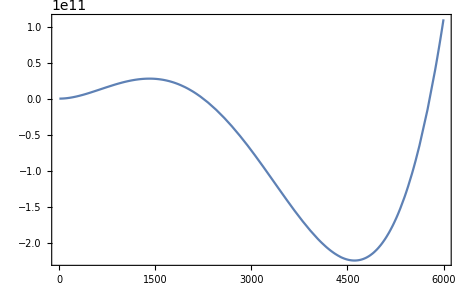

```mathematica
Plot[VBParwani[0.016,ϕ,4505.],{ϕ,0,6000}]
```

```mathematica
T1=4505.0;
fitting=Table[{ϕ,VBParwani[0.016,ϕ,T1]},{ϕ,1,6000,10}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
xr=x/.Minimize[{Vfit[x]-Vfit[0],{3000<x<6000}},x][[2]];
SbyT=(FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}]/T1)[[1]]
```

.......................

138.085

........................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................

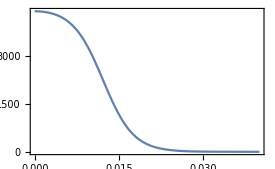

```mathematica
Plot[FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}][[2]][r],{r,0,0.04}]
```

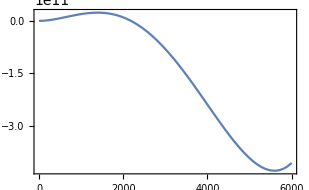

```mathematica
Plot[VeffParwani[0.009,ϕ,3695.],{ϕ,0,6000}]
```

```mathematica
T1=3687.2;
fitting=Table[{ϕ,VeffParwani[0.009,ϕ,T1]},{ϕ,1,6000,10}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
xr=x/.Minimize[{Vfit[x]-Vfit[0],{3000<x<6000}},x][[2]];
SbyT=(FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}]/T1)[[1]]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

...............................

139.133

................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

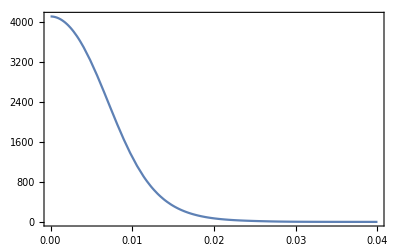

```mathematica
Plot[FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}][[2]][r],{r,0,0.04}]
```